### Quantum Cloning

```mathematica
(*Partial trace function*)
SwapParts[expr_,pos1_,pos2_]:=ReplacePart[#,#,{pos1,pos2},{pos2,pos1}]&[expr]
TraceSystem[D_,s_]:=(Qubits=Reverse[Sort[s]];
TrkM=D;
z=(Dimensions[Qubits][[1]]+1);
For[q=1,q<z,q++,n=Log[2,(Dimensions[TrkM][[1]])];
M=TrkM;
k=Qubits[[q]];
If[k==n,TrkM={};
For[p=1,p<2^n+1,p=p+2,TrkM=Append[TrkM,Take[M[[p,All]],{1,2^n,2}]+Take[M[[p+1,All]],{2,2^n,2}]];],For[j=0,j<(n-k),j++,b={0};
For[i=1,i<2^n+1,i++,If[(Mod[(IntegerDigits[i-1,2,n][[n]]+IntegerDigits[i-1,2,n][[n-j-1]]),2])==1&&Count[b,i]==0,Permut={i,(FromDigits[SwapParts[(IntegerDigits[i-1,2,n]),{n},{n-j-1}],2]+1)};
b=Append[b,(FromDigits[SwapParts[(IntegerDigits[i-1,2,n]),{n},{n-j-1}],2]+1)];
c=Range[2^n];
perm=SwapParts[c,{i},{(FromDigits[SwapParts[(IntegerDigits[i-1,2,n]),{n},{n-j-1}],2]+1)}];
M=M[[perm,perm]];]];
TrkM={};
For[p=1,p<2^n+1,p=p+2,TrkM=Append[TrkM,Take[M[[p,All]],{1,2^n,2}]+Take[M[[p+1,All]],{2,2^n,2}]];]];]];Return[TrkM]);
```

```mathematica
(*Definitions*)
u={{1},{0}};
d={{0},{1}};
(*Position dependent spin initialisations*)
sp[i_,0]:=u;
sp[i_,1]:=d;
```

```mathematica
(*Spin configurations*)

(*Starting from the state (α|01⟩+β|10⟩) (|01⟩- |10⟩)/√2 (|01⟩- |10⟩)/√2,we obtain 8 possible spin configurations.The first 4 correspond to the α branch and the last 4 to the β branch,following the (+--+) and (+--+) order respectively.*)

spins={{0,1,0,1,0,1},{0,1,1,0,0,1},{0,1,0,1,1,0},{0,1,1,0,1,0},{1,0,0,1,0,1},{1,0,1,0,0,1},{1,0,0,1,1,0},{1,0,1,0,1,0}};

(*State based on position list*)
State[spinConfig_List,pos_List]:=KroneckerProduct@@Table[sp[i,spinConfig[[pos[[i]]]]],{i,6}];

(*Position order*)
pos={1,2,3,4,5,6};

(*initial state*)
ξ=α/2 (State[spins[[1]],pos]-State[spins[[2]],pos]-State[spins[[3]],pos]+State[spins[[4]],pos])+β/2 (State[spins[[5]],pos]-State[spins[[6]],pos]-State[spins[[7]],pos]+State[spins[[8]],pos]);
```

```mathematica
MatrixForm[State[spins[[1]],pos]]
```

(0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
1
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0)

```mathematica
Dimensions[%11]
```

{64,1}

```mathematica
(*Define the Beam Splitter action;|s_1> ->Sqrt[1-R]|s_1'>+i Sqrt[R]|s_3'>;|s_3> ->Sqrt[1-R]|s_3'>+i Sqrt[R]|s_1'>;|s_2> ->Sqrt[1-R]|s_2'>+i Sqrt[R]|s_5'>;|s_5> ->Sqrt[1-R]|s_5'>+i Sqrt[R]|s_2'>;
We have a six-qubit state,so we can write it as:
|s_1>|s_2>|s_3>|s_4>|s_5>|s_6>,where each position s_1 to s_6 may take a different spin value.After the action of the BS unitary:
|s_1>|s_2>|s_3>|s_4>|s_5>|s_6> ->(Sqrt[1-R]|s_1'>+i Sqrt[R]|s_3'>) (Sqrt[1-R]|s_2'>+i Sqrt[R]|s_5'>) (Sqrt[1-R]|s_3'>+i Sqrt[R]|s_1'>)... (and similarly for s_4,s_5,s_6) 
|s_1>|s_2>|s_3>|s_4>|s_5>|s_6> ->(1-R)^2|s_1'>|s_2'>|s_3'>|s_4'>|s_5'>|s_6'>-R (1-R)|s_3'>|s_2'>|s_1'>|s_4'>|s_5'>|s_6'>+R^2|s_3'>|s_5'>|s_1'>|s_4'>|s_2'>|s_6'>;*)

(*Define the Beam splitter action;
|s>_1-> √(1-R)|s>_(1')+i √R|s>_(3');|s>_3-> √(1-R)|s>_(3')+i √R|s>_(1');|s>_2-> √(1-R)|s>_(2')+i √R|s>_(5');|s>_(5')-> √(1-R)|s>_(5')+i √R|s>_(2');

We have a six qubit state, so we can write this like 
|Subscript[s, 1]>_1|Subscript[s, 2]>_2|Subscript[s, 3]>_3|Subscript[s, 4]>_4|Subscript[s, 5]>_5|Subscript[s, 6]>_6; each position can take different spin so in general Subscript[s, 1] to Subscript[s, 6] may be different; 

After the action of BS\unitary ;
|Subscript[s, 1]>_1|Subscript[s, 2]>_2|Subscript[s, 3]>_3|Subscript[s, 4]>_4|Subscript[s, 5]>_5|Subscript[s, 6]>_6 -> (|√(1-R)|Subscript[s, 1]>_(1')+i √R|Subscript[s, 1]>_(3'))(|√(1-R)|Subscript[s, 2]>_(2')+i √R|Subscript[s, 2]>_(5'))(|√(1-R)|Subscript[s, 3]>_(3')+i √R|Subscript[s, 3]>_(1'))Subscript[s, 4](|√(1-R)|Subscript[s, 5]>_(5')+i √R|Subscript[s, 5]>_(2'))Subscript[s, 6];
Some terms like i √R √(1-R)|Subscript[s, 1]>_(1')|Subscript[s, 1]>_(1')and other combinations occur,where two photons appear in a single mode.

In our calculation, we consider only single-photon-per-mode terms,discarding all terms where multiple photons occupy the same mode.This is equivalent to post-selecting our system to states where each mode contains exactly one photon.Then the unnormalized post-selected state is given by:

|Subscript[s, 1]>_1|Subscript[s, 2]>_2|Subscript[s, 3]>_3|Subscript[s, 4]>_4|Subscript[s, 5]>_5|Subscript[s, 6]>_6 -> (1-R)^2|Subscript[s, 1]>_(1')|Subscript[s, 2]>_(2')|Subscript[s, 3]>_(3')|Subscript[s, 4]>_4|Subscript[s, 5]>_(5')|Subscript[s, 6]>_6 -R(1-R)|Subscript[s, 3]>_(1')|Subscript[s, 2]>_(2')|Subscript[s, 1]>_(3')|Subscript[s, 4]>_4|Subscript[s, 5]>_(5')|Subscript[s, 6]>_6 -R(1-R)|Subscript[s, 1]>_(1')|Subscript[s, 5]>_(2')|Subscript[s, 3]>_(3')|Subscript[s, 4]>_4|Subscript[s, 2]>_(5')|Subscript[s, 6]>_6+R^2|Subscript[s, 3]>_(1')|Subscript[s, 5]>_(2')|Subscript[s, 1]>_(3')|Subscript[s, 4]>_4|Subscript[s, 2]>_(5')|Subscript[s, 6]>_6;
*)

BSUpdatedState[spinConfig_,pos_,R_]:=Module[{s},s=Table[sp[i,spinConfig[[pos[[i]]]]],{i,6}];(1-R)^2*KroneckerProduct[s[[1]],s[[2]],s[[3]],s[[4]],s[[5]],s[[6]]]-(1-R) R*KroneckerProduct[s[[3]],s[[2]],s[[1]],s[[4]],s[[5]],s[[6]]]-(1-R) R*KroneckerProduct[s[[1]],s[[5]],s[[3]],s[[4]],s[[2]],s[[6]]]+R^2*KroneckerProduct[s[[3]],s[[5]],s[[1]],s[[4]],s[[2]],s[[6]]]]
```

```mathematica
(*Final state in 1'2'3'45'6*)
ξfinal=(α/2) (BSUpdatedState[spins[[1]],pos,R]-BSUpdatedState[spins[[2]],pos,R]-BSUpdatedState[spins[[3]],pos,R]+BSUpdatedState[spins[[4]],pos,R])+(β/2) (BSUpdatedState[spins[[5]],pos,R]-BSUpdatedState[spins[[6]],pos,R]-BSUpdatedState[spins[[7]],pos,R]+BSUpdatedState[spins[[8]],pos,R]);
ξfinalT= Transpose[ξfinal](*ConjugateTranspose[ξfinal]*);
ρξfinal = ξfinal.ξfinalT;
Simplify[Tr[ρξfinal]]
ρξfinal=ρξfinal/Tr[ρξfinal];


ρ12=FullSimplify[TraceSystem[ρξfinal,{3,4,5,6}]];
ρ46 = FullSimplify[TraceSystem[ρξfinal,{1,2,3,5}]];
β=√(1-α^2);
(*Maximally entangled state*)
ϕ=FullSimplify[α*KroneckerProduct[u, d] +√(1-α^2)*KroneckerProduct[d,u],0<=α<=1];ϕT =FullSimplify[ConjugateTranspose[ϕ],0<=α<=1];
ρϕ= FullSimplify[ϕ . ϕT];
ρϕ= ρϕ/Tr[ρϕ];

F12[α_,R_]:=FullSimplify[Tr[ρϕ.ρ12]];

F46[α_,R_]:=FullSimplify[Tr[ρϕ.ρ46]];
Plot3D[{F12[α,R],F46[α,R]},{α,0,1},{R,0,1},PlotRange->All,PlotLegends->{"F_(1' 2')","F_46"}]
```

(1-3 R+3 R^2)^2

-Graphics3D-

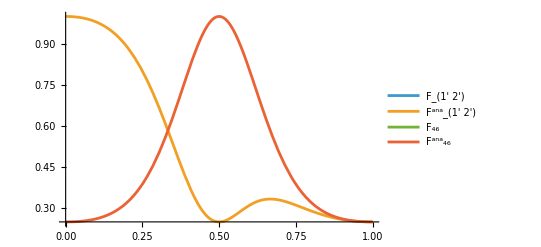

```mathematica
(*Analytical expression form paper for α=1/(√2) case*)
F12ana=(2 (1-2 R)^2 (1-R)^2+(2-12 R+28 R^2-30 R^3+13 R^4))/(4 (3 R^2-3 R+1)^2);

F46ana=(2 R^2 (1-R)^2+(1-6 R+16 R^2-20 R^3+10 R^4))/(4 (3 R^2-3 R+1)^2);
Plot[{F12[1/(√2),R],F12ana, F46[1/(√2),R],F46ana},{R,0,1},PlotRange->All,PlotLegends->{"F_(1' 2')","(F^ana)_(1' 2')","F_46","(F^ana)_46"}]
```

#### Genuine entanglement Cloning - GHZ (Type-I)

Start from a general GHZ or W-state, three maximally entangled Bell states. Apply Beam Splitter operation as above and see whether the post measured clone state have good fidelity or not. Early pioneering work by Kuang et al. (2000) demonstrated that GHZ state entanglement can be partially broadcasted through both local and non-local copying processes, with non-local cloning proving more efficient. If above method works, then we can extend it to multipartite case as follows and generalise the results

In case it doesn’t work, we can use multiport splitter operation and maximally entangled GHZ and W-state as auxiliary state as follows:

There is a possibility three cloned states also check if that is the case. In the above case, you may apply two port beam splitter operation (U1) also and compare the result w.r.t. maximally entangled Bell state as auxiliary state.